```mathematica
FourierTransform[1/(kx^2+ky^2),{kx,ky},{x,y}]
```

1/2 (-HeavisideTheta[-x] (2 EulerGamma+2 Log[-x]+Log[1+y^2/x^2])-HeavisideTheta[x] (2 EulerGamma+2 Log[x]+Log[1+y^2/x^2]))

```mathematica
ft01=-EulerGamma-Log[r]
```

-EulerGamma-Log[r]

We would like to evalue the Fourier Transform of

```mathematica
itg:=1/(kx^2+ky^2)1/((kx-lx)^2+(ky-ly)^2)
```

```mathematica
FourierTransform[1/(kx^2+ky^2)1/((kx-lx)^2+(ky-ly)^2),{kx,ky},{x,y}]
```

$Aborted

Since it is scalar, we put set {x,y}/r as the y axis with r the modulus of {x,y}. Then it is trivial to integrate out kx firxt.

It is trivial to integrate out, say, kx :

```mathematica
intkxana[ky_,{lx_,ly_}]=FullSimplify[I HeavisideTheta[ky]Residue[itg,{kx,I ky}]]+FullSimplify[I HeavisideTheta[-ky]Residue[itg,{kx,-I ky}]]+FullSimplify[I HeavisideTheta[ky-ly]Residue[itg,{kx,lx+I (ky-ly)}]]+FullSimplify[I HeavisideTheta[-ky+ly]Residue[itg,{kx,lx-I (ky-ly)}]]
```

(ⅈ HeavisideTheta[-ky])/(2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly))+(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))+HeavisideTheta[ky-ly]/(2 (ky-ly) (2 ky-ⅈ lx-ly) (ⅈ lx+ly))-HeavisideTheta[-ky+ly]/(2 (ky-ly) (lx+ⅈ ly) (-2 ⅈ ky+lx+ⅈ ly))

```mathematica
ftkx:=(ⅈ HeavisideTheta[-ky])/(2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly))+(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))+HeavisideTheta[ky-ly]/(2 (ky-ly) (2 ky-ⅈ lx-ly) (ⅈ lx+ly))-HeavisideTheta[-ky+ly]/(2 (ky-ly) (lx+ⅈ ly) (-2 ⅈ ky+lx+ⅈ ly))
```

```mathematica
intkx[ky_,{lx_,ly_}]:=1/(2π)NIntegrate[1/(kx^2+ky^2)1/((kx-lx)^2+(ky-ly)^2),{kx,-Infinity,Infinity}]
```

```mathematica
cond:=r>0&&x∈Reals&&y∈Reals&&2 π>ϕ>0 &&ky∈Reals&&lx∈Reals&&ly∈Reals
```

the first term

#### Term 1

```mathematica
ftkx[[1]]
```

(ⅈ HeavisideTheta[-ky])/(2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly))

```mathematica
dem:=2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly)
```

```mathematica
apky= Apart[((lx-ⅈ ly) (lx+ⅈ ly))/dem,ky]
```

ⅈ/(2 ky)-ⅈ/(2 ky-ⅈ lx-ly)

```mathematica
term11=Assuming[cond,1/l^2 FourierTransform[ftkx[[1]] dem apky[[1]],ky,r]//FullSimplify]
```

-(EulerGamma+(ⅈ π)/2+Log[r])/(2 l^2 √(2 π))

```mathematica
ftkx[[1]] dem apky[[2]]
```

HeavisideTheta[-ky]/(2 ky-ⅈ lx-ly)

```mathematica
Numerator[ftkx[[1]] dem apky[[2]]]
```

HeavisideTheta[-ky]

```mathematica
FullSimplify[Expand[√(2 π)FourierTransform[HeavisideTheta[-ky],ky,y]]]
Assuming[cond,FullSimplify[Expand[√(2 π)FourierTransform[1/(2 ky-ⅈ lx-ly),ky,y]]]]
```

-ⅈ/y+π DiracDelta[y]

ⅈ ⅇ^(-1/2 (lx-ⅈ ly) y) π HeavisideTheta[y Sign[lx]] Sign[lx]

```mathematica
Integrate[ⅈ ⅇ^(-1/2 (lx-ⅈ ly) y) π HeavisideTheta[y ](-ⅈ/(r-y)+π DiracDelta[r-y]) ,{y,-Infinity,Infinity}]
Integrate[-ⅈ ⅇ^(-1/2 (lx-ⅈ ly) y) π HeavisideTheta[-y ](-ⅈ/(r-y)+π DiracDelta[r-y]) ,{y,-Infinity,Infinity}]
```

ConditionalExpression[-ⅇ^(-1/2 (lx-ⅈ ly) r) π Gamma[0,-1/2 (lx-ⅈ ly) r],Im[ly]+Re[lx]>0&&Re[r]<0&&Im[r]==0]

ConditionalExpression[-ⅇ^(-1/2 (lx-ⅈ ly) r) π Gamma[0,-1/2 (lx-ⅈ ly) r],Im[ly]+Re[lx]<0&&Re[r]>0&&Im[r]==0]

```mathematica
t12:=-1/(2 π Sqrt[2π] l^2)ⅇ^(-1/2 (lx-ⅈ ly) r) π Gamma[0,-1/2 (lx-ⅈ ly) r]
```

```mathematica
term1=term11+t12
```

-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx-ⅈ ly) r])/(2 l^2 √(2 π))-(EulerGamma+(ⅈ π)/2+Log[r])/(2 l^2 √(2 π))

#### Term 2

```mathematica
ftkx
```

(ⅈ HeavisideTheta[-ky])/(2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly))+(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))+HeavisideTheta[ky-ly]/(2 (ky-ly) (2 ky-ⅈ lx-ly) (ⅈ lx+ly))-HeavisideTheta[-ky+ly]/(2 (ky-ly) (lx+ⅈ ly) (-2 ⅈ ky+lx+ⅈ ly))

```mathematica
ftkx[[2]]
```

(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))

```mathematica
Denominator[ftkx[[2]]]
```

2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly)

```mathematica
apky= Apart[((lx-ⅈ ly) (lx+ⅈ ly))/Denominator[ftkx[[2]]],ky]
```

-ⅈ/(2 ky)+ⅈ/(2 ky+ⅈ lx-ly)

```mathematica
Numerator[ftkx[[2]]] apky[[1]]
```

HeavisideTheta[ky]/(2 ky)

```mathematica
term21=Assuming[cond,1/l^2 FourierTransform[Numerator[ftkx[[2]]] apky[[1]],ky,r]//FullSimplify]
```

(ⅈ (2 ⅈ EulerGamma+π+2 ⅈ Log[r]))/(4 l^2 √(2 π))

```mathematica
term22=Assuming[cond,1/(lx^2+ly^2)FourierTransform[Numerator[ftkx[[2]]]apky[[2]],ky,r]//FullSimplify]
```

1/(4 (lx^2+ly^2) √(2 π))ⅇ^(1/2 (lx+ⅈ ly) r) (-ⅈ π+2 CosIntegral[1/2 ⅈ (lx+ⅈ ly) r]-2 SinhIntegral[1/2 (lx+ⅈ ly) r])

```mathematica
FullSimplify[Expand[√(2 π)FourierTransform[Numerator[ftkx[[2]]] ,ky,y]]]
Assuming[cond,FullSimplify[Expand[√(2 π)FourierTransform[apky[[2]],ky,y]]]]
```

-1/y+ⅈ π DiracDelta[y]

ⅇ^(1/2 (lx+ⅈ ly) y) π HeavisideTheta[-y Sign[lx]] Sign[lx]

```mathematica
Integrate[ⅇ^(1/2 (lx+ⅈ ly) y) π HeavisideTheta[-y ] (-1/(r-y)+ⅈ π DiracDelta[r-y]) ,{y,-Infinity,Infinity}]
Integrate[-ⅇ^(1/2 (lx+ⅈ ly) y) π HeavisideTheta[y](-1/(r-y)+ⅈ π DiracDelta[r-y]) ,{y,-Infinity,Infinity}]
```

ConditionalExpression[-ⅇ^(1/2 (lx+ⅈ ly) r) π Gamma[0,1/2 (lx+ⅈ ly) r],Re[lx]>Im[ly]&&Re[r]>0&&Im[r]==0]

ConditionalExpression[-ⅇ^(1/2 (lx+ⅈ ly) r) π Gamma[0,1/2 (lx+ⅈ ly) r],Re[lx]<Im[ly]&&Re[r]<0&&Im[r]==0]

```mathematica
t22:=1/(2 π Sqrt[2π] l^2)(-ⅇ^(1/2 (lx+ⅈ ly) r) π Gamma[0,1/2 (lx+ⅈ ly) r])
```

```mathematica
term22/.{lx->3,ly->0.3,r->1.0}
t22/.{lx->3,ly->0.3,r->1.0}
```

-0.00978113+0.000714427 ⅈ

-0.00978113+0.000714427 ⅈ

```mathematica
term2=term21+t22
```

-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r])/(2 l^2 √(2 π))+(ⅈ (2 ⅈ EulerGamma+π+2 ⅈ Log[r]))/(4 l^2 √(2 π))

```mathematica
ftkx[[1;;2]]
```

(ⅈ HeavisideTheta[-ky])/(2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly))+(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))

From this, we can see how the two related to each other :

```mathematica
(Assuming[cond,Conjugate[ftkx[[1]]]//FullSimplify]/.Conjugate[x_]->x/.{ky->-ky}//FullSimplify)/.{lx->-lx,ly->-ly}//FullSimplify
```

(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))

```mathematica
(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))-ftkx[[2]]
```

0

```mathematica
((Assuming[cond&&l>0,Conjugate[term1]//FullSimplify])/.{lx->-lx,ly->-ly}//FullSimplify)/.Conjugate[Gamma[0,1/2 (lx-ⅈ ly) r]]->Gamma[0,1/2 (lx+ⅈ ly) r]
```

-(2 EulerGamma-ⅈ π+2 ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r]+2 Log[r])/(4 l^2 √(2 π))

```mathematica
-(2 EulerGamma-ⅈ π+2 ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r]+2 Log[r])/(4 l^2 √(2 π))-term2//FullSimplify
```

0

Check!

#### Term 3

```mathematica
ftkx
```

(ⅈ HeavisideTheta[-ky])/(2 ky (2 ky-ⅈ lx-ly) (lx+ⅈ ly))+(ⅈ HeavisideTheta[ky])/(2 ky (2 ky+ⅈ lx-ly) (lx-ⅈ ly))+HeavisideTheta[ky-ly]/(2 (ky-ly) (2 ky-ⅈ lx-ly) (ⅈ lx+ly))-HeavisideTheta[-ky+ly]/(2 (ky-ly) (lx+ⅈ ly) (-2 ⅈ ky+lx+ⅈ ly))

```mathematica
((FullSimplify[(ftkx[[3]]/.{ky->ky+ly})]))-(ftkx[[2]]/.{lx->-lx,ly->-ly})//FullSimplify
```

0

This tells us that

```mathematica
term3=FullSimplify[Exp[I ly r] (term2/.{lx->-lx,ly->-ly})]
```

-(ⅇ^(ⅈ ly r) (2 EulerGamma-ⅈ π+2 ⅇ^(-1/2 (lx+ⅈ ly) r) Gamma[0,-1/2 (lx+ⅈ ly) r]+2 Log[r]))/(4 l^2 √(2 π))

#### Term 4

```mathematica
((FullSimplify[(ftkx[[4]]/.{ky->ky+ly})]))-(ftkx[[1]]/.{lx->-lx,ly->-ly})//FullSimplify
```

0

```mathematica
term4=FullSimplify[Exp[I ly r] (term1/.{lx->-lx,ly->-ly})]
```

-(ⅇ^(ⅈ ly r) (2 EulerGamma+ⅈ π+2 ⅇ^(1/2 (lx-ⅈ ly) r) Gamma[0,1/2 (lx-ⅈ ly) r]+2 Log[r]))/(4 l^2 √(2 π))

```mathematica
cond
```

r>0&&x∈Reals&&y∈Reals&&2 π>ϕ>0&&ky∈Reals&&lx∈Reals&&ly∈Reals

#### Final

```mathematica
final=Expand[Assuming[cond,Simplify[Sqrt[2π] (term1+term2+term3+term4)]]]
```

-EulerGamma/l^2-(ⅇ^(ⅈ ly r) EulerGamma)/l^2-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx-ⅈ ly) r])/(2 l^2)-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx-ⅈ ly) r])/(2 l^2)-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx+ⅈ ly) r])/(2 l^2)-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r])/(2 l^2)-Log[r]/l^2-(ⅇ^(ⅈ ly r) Log[r])/l^2

Note that this is the result for ϕx = π/2. lx=l cos(ϕl-π/2) and ly=l sin(ϕl-π/2).

```mathematica
ft02[{l_,ϕl_},{r_,ϕx_}]=((-EulerGamma/l^2-(ⅇ^(ⅈ ly r) EulerGamma)/l^2-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx-ⅈ ly) r])/(2 l^2)-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx-ⅈ ly) r])/(2 l^2)-(ⅇ^(-1/2 (lx-ⅈ ly) r) Gamma[0,-1/2 (lx+ⅈ ly) r])/(2 l^2)-(ⅇ^(1/2 (lx+ⅈ ly) r) Gamma[0,1/2 (lx+ⅈ ly) r])/(2 l^2)-Log[r]/l^2-(ⅇ^(ⅈ ly r) Log[r])/l^2)/.{lx->l Cos[ϕl-ϕx+π/2],ly->l Sin[ϕl-ϕx+π/2]})
```

-EulerGamma/l^2-(ⅇ^(ⅈ l r Cos[ϕl-ϕx]) EulerGamma)/l^2-(ⅇ^(-1/2 r (-ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])) Gamma[0,-1/2 r (-ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])])/(2 l^2)-(ⅇ^(1/2 r (ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])) Gamma[0,1/2 r (-ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])])/(2 l^2)-(ⅇ^(-1/2 r (-ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])) Gamma[0,-1/2 r (ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])])/(2 l^2)-(ⅇ^(1/2 r (ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])) Gamma[0,1/2 r (ⅈ l Cos[ϕl-ϕx]-l Sin[ϕl-ϕx])])/(2 l^2)-Log[r]/l^2-(ⅇ^(ⅈ l r Cos[ϕl-ϕx]) Log[r])/l^2

```mathematica
ft01[{l_,ϕl_},{r_,ϕx_}]=(-EulerGamma-Log[r])/l^2
```

(-EulerGamma-Log[r])/l^2

```mathematica
F01[{x_,y_},{kx_,ky_}]:=Module[{r,ϕx,l,ϕk},
r=Sqrt[x^2+y^2];ϕx=ArcTan[x,y];
l=Sqrt[kx^2+ky^2];ϕk=ArcTan[kx,ky];
ft01[{l,ϕk},{r,ϕx}]
]
F02[{x_,y_},{kx_,ky_}]:=Module[{r,ϕx,l,ϕk},
r=Sqrt[x^2+y^2];ϕx=ArcTan[x,y];
l=Sqrt[kx^2+ky^2];ϕk=ArcTan[kx,ky];
ft02[{l,ϕk},{r,ϕx}]
]
```

```mathematica
ana[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{lx_,ly_}]:=( F01[{bx+x1-x3,by+y1-y3},{lx,ly}] Exp[-I (lx x1+ly y1)]-F01[{bx-x3+x2,by-y3+y2},{lx,ly}] Exp[-I (lx x2+ly y2)]-F01[{bx-x4+x1,by-y4+y1},{lx,ly}] Exp[-I (lx x1+ly y1)]+F01[{bx-x4+x2,by-y4+y2},{lx,ly}] Exp[-I (lx x2+ly y2)])-( F02[{bx+x1-x3,by+y1-y3},{lx,ly}] Exp[-I (lx x1+ly y1)]-F02[{bx-x3+x2,by-y3+y2},{lx,ly}] Exp[-I (lx x2+ly y2)]-F02[{bx-x4+x1,by-y4+y1},{lx,ly}] Exp[-I (lx x1+ly y1)]+F02[{bx-x4+x2,by-y4+y2},{lx,ly}] Exp[-I (lx x2+ly y2)])
```

```mathematica
num[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{lx_,ly_}]:=1/(2π)NIntegrate[Exp[I (bx kx+by ky)] 1/(kx^2+ky^2)(1/(lx^2+ly^2)-1/((kx-lx)^2+(ky-ly)^2)) (Exp[-I (kx x3+ ky y3)]-Exp[-I (kx x4+ ky y4)])(Exp[I ((kx-lx) x1+ (ky-ly) y1)]-Exp[I ((kx-lx) x2+ (ky-ly) y2)]),{kx,-Infinity,Infinity},{ky,-Infinity,Infinity}]
```

```mathematica
bu={3.0,0.1};
x1u={1.0,0.5};
x2u={1.5,0.25};
x3u={0.1,0.75};
x4u={1.3,2.5};
ku={2.2,1.8};
num[bu,x1u,x2u,x3u,x4u,{2.2,1.8}]
```

0.00511557+0.00174474 ⅈ

```mathematica
ana[bu,x1u,x2u,x3u,x4u,ku]
```

0.00511521+0.00174514 ⅈ

```mathematica
bu={1.0,-0.1};
x1u={1.3,0.45};
x2u={0.5,0.125};
x3u={0.31,0.5};
x4u={3.3,.5};
ku={2.3,0.8};
num[bu,x1u,x2u,x3u,x4u,ku]
ana[bu,x1u,x2u,x3u,x4u,ku]
```

0.289065+0.303098 ⅈ

0.289015+0.303045 ⅈ

## Dipole Radiation

```mathematica
F01R[{x_,y_},{kx_,ky_}]=Simplify[{kx,ky} F01[{x,y},{kx,ky}]]
```

{-(kx (2 EulerGamma+Log[x^2+y^2]))/(2 (kx^2+ky^2)),-(ky (2 EulerGamma+Log[x^2+y^2]))/(2 (kx^2+ky^2))}

```mathematica
F02R[{x_,y_},{kx_,ky_}]=Simplify[{kx,ky}F02[{x,y},{kx,ky}]+I{D[F02[{x,y},{kx,ky}],x],D[F02[{x,y},{kx,ky}],y]}]
```

{1/(4 (kx^2+ky^2))ⅇ^(1/2 (-ky x-kx y)) (-4 ⅇ^(1/2 (ky x+kx y)) EulerGamma kx-ⅇ^((ⅈ kx x)/2+ky x+(ⅈ ky y)/2) (kx+ⅈ ky) Gamma[0,1/2 (-ⅈ kx+ky) (x-ⅈ y)]-ⅇ^((ⅈ kx x)/2+ky x+(ⅈ ky y)/2) (kx+ⅈ ky) Gamma[0,1/2 (ⅈ kx+ky) (x+ⅈ y)]-ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) kx Gamma[0,1/2 (kx-ⅈ ky) (-ⅈ x+y)]+ⅈ ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) ky Gamma[0,1/2 (kx-ⅈ ky) (-ⅈ x+y)]-ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) kx Gamma[0,1/2 (kx+ⅈ ky) (ⅈ x+y)]+ⅈ ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) ky Gamma[0,1/2 (kx+ⅈ ky) (ⅈ x+y)]-2 ⅇ^(1/2 (ky x+kx y)) kx Log[x^2+y^2]),1/(4 (kx^2+ky^2))ⅇ^(1/2 (-ky x-kx y)) (-4 ⅇ^(1/2 (ky x+kx y)) EulerGamma ky+ⅈ ⅇ^((ⅈ kx x)/2+ky x+(ⅈ ky y)/2) (kx+ⅈ ky) Gamma[0,1/2 (-ⅈ kx+ky) (x-ⅈ y)]+ⅈ ⅇ^((ⅈ kx x)/2+ky x+(ⅈ ky y)/2) (kx+ⅈ ky) Gamma[0,1/2 (ⅈ kx+ky) (x+ⅈ y)]-ⅈ ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) kx Gamma[0,1/2 (kx-ⅈ ky) (-ⅈ x+y)]-ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) ky Gamma[0,1/2 (kx-ⅈ ky) (-ⅈ x+y)]-ⅈ ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) kx Gamma[0,1/2 (kx+ⅈ ky) (ⅈ x+y)]-ⅇ^((ⅈ kx x)/2+kx y+(ⅈ ky y)/2) ky Gamma[0,1/2 (kx+ⅈ ky) (ⅈ x+y)]-2 ⅇ^(1/2 (ky x+kx y)) ky Log[x^2+y^2])}

```mathematica
numx[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{lx_,ly_}]:=NIntegrate[Exp[I (bx kx+by ky)] 1/(kx^2+ky^2)(lx/(lx^2+ly^2)-(lx-kx)/((kx-lx)^2+(ky-ly)^2)) (Exp[-I (kx x3+ ky y3)]-Exp[-I (kx x4+ ky y4)])(Exp[I ((kx-lx) x1+ (ky-ly) y1)]-Exp[I ((kx-lx) x2+ (ky-ly) y2)]),{kx,-Infinity,Infinity},{ky,-Infinity,Infinity}]
numy[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{lx_,ly_}]:=NIntegrate[Exp[I (bx kx+by ky)] 1/(kx^2+ky^2)(ly/(lx^2+ly^2)-(ly-ky)/((kx-lx)^2+(ky-ly)^2)) (Exp[-I (kx x3+ ky y3)]-Exp[-I (kx x4+ ky y4)])(Exp[I ((kx-lx) x1+ (ky-ly) y1)]-Exp[I ((kx-lx) x2+ (ky-ly) y2)]),{kx,-Infinity,Infinity},{ky,-Infinity,Infinity}]
ana[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=2π(( F01R[{bx+x1-x3,by+y1-y3},{kx,ky}] Exp[-I (kx x1+ky y1)]-F01R[{bx-x3+x2,by-y3+y2},{kx,ky}] Exp[-I (kx x2+ky y2)]-F01R[{bx-x4+x1,by-y4+y1},{kx,ky}] Exp[-I (kx x1+ky y1)]+F01R[{bx-x4+x2,by-y4+y2},{kx,ky}] Exp[-I (kx x2+ky y2)])-( F02R[{bx+x1-x3,by+y1-y3},{kx,ky}] Exp[-I (kx x1+ky y1)]-F02R[{bx-x3+x2,by-y3+y2},{kx,ky}] Exp[-I (kx x2+ky y2)]-F02R[{bx-x4+x1,by-y4+y1},{kx,ky}] Exp[-I (kx x1+ky y1)]+F02R[{bx-x4+x2,by-y4+y2},{kx,ky}] Exp[-I (kx x2+ky y2)]))
```

```mathematica
bu={1.0,-0.1};
x1u={1.3,0.45};
x2u={0.5,0.125};
x3u={0.31,0.5};
x4u={3.3,.5};
ku={2.3,0.8};
{numx[bu,x1u,x2u,x3u,x4u,ku],numy[bu,x1u,x2u,x3u,x4u,ku]}
ana[bu,x1u,x2u,x3u,x4u,ku]
```

{1.10543+1.10826 ⅈ,0.685803+1.1379 ⅈ}

{1.10543+1.10826 ⅈ,0.685803+1.1379 ⅈ}

```mathematica
dσ[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=ana[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
showdσ[bu_,x1u_,x2u_,x3u_,x4u_,kT_]:=Module[{ϕ},
Print[Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x3u,bu+x4u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x4u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"]];
Print[""];
Print[ParametricPlot[dσ[bu,x1u,x2u,x3u,x4u,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16},PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"]];
Print["v_2=",NIntegrate[dσ[bu,x1u,x2u,x3u,x4u,{kT,ϕ}] Cos[2(ϕ)],{ϕ,0,2π}]/NIntegrate[dσ[bu,x1u,x2u,x3u,x4u,{kT,ϕ}],{ϕ,0,2π}]];
]
```

### kT~1/r

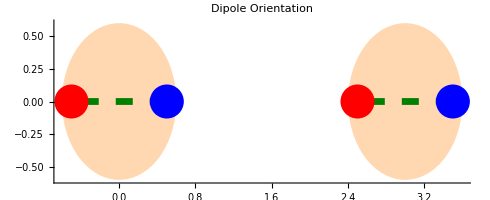

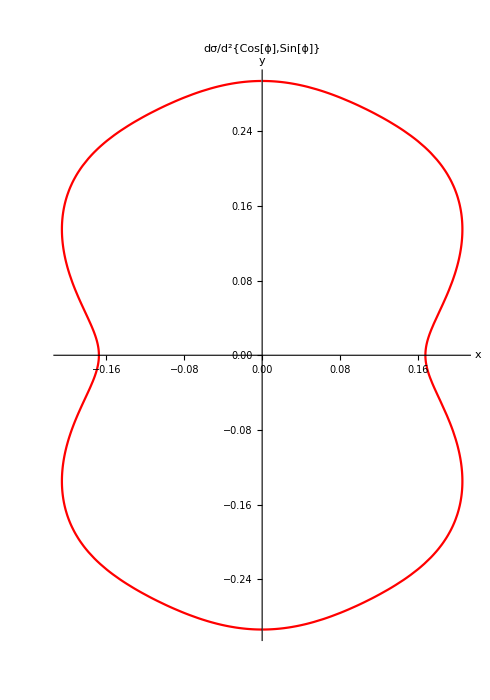

v_2=-0.114285-4.15293×10^-20 ⅈ

```mathematica
x1u={1/2,0};
x2u={-1/2,0};
x3u={1/2,0};
x4u={-1/2,0};
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

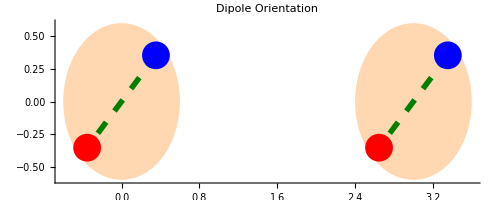

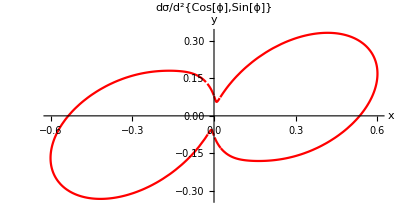

v_2=0.364805+1.18451×10^-18 ⅈ

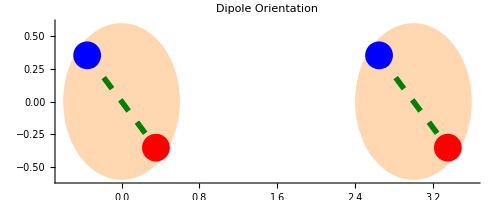

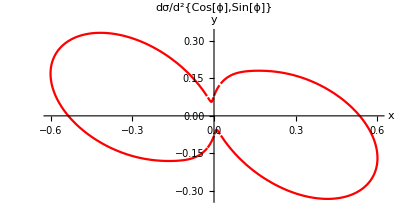

v_2=0.364805+3.09828×10^-18 ⅈ

```mathematica
x1u={1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
x1u={-1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

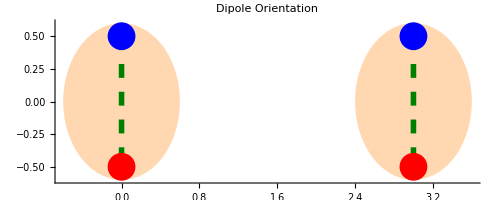

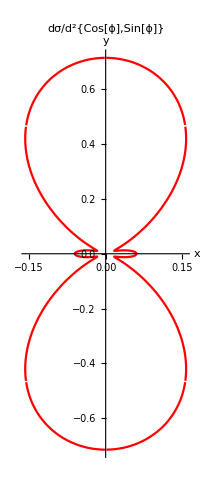

v_2=-0.669888-3.62969×10^-18 ⅈ

```mathematica
x1u={0,1/2};
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=1.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

Therefore, we have v2 in hadron - hadron collisions.

### kT>>1/r

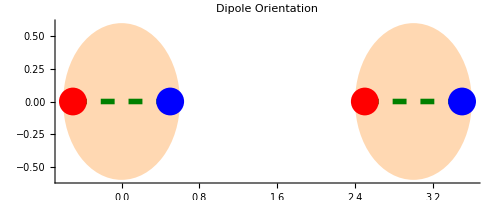

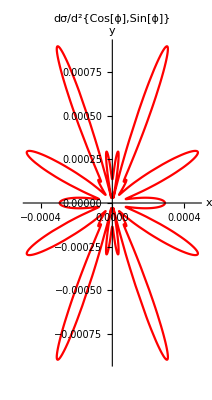

v_2=-0.0641272+0. ⅈ

```mathematica
x1u={1/2,0};
x2u={-1/2,0};
x3u={1/2,0};
x4u={-1/2,0};
bu={3,0};
kT=10.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

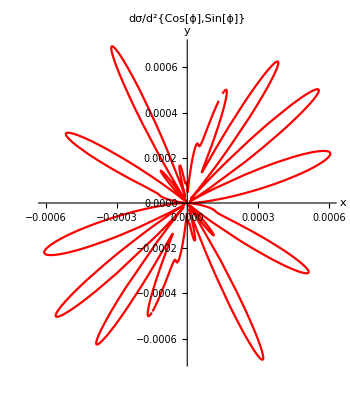

v_2=-0.0142743+0. ⅈ

-Graphics-

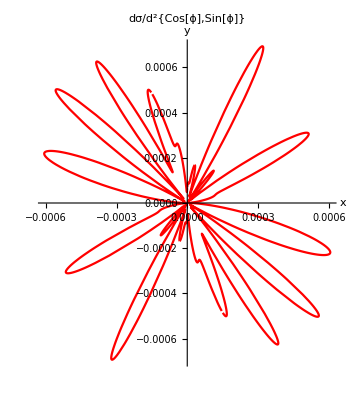

v_2=-0.0142743+0. ⅈ

```mathematica
kT=10.0;
x1u={1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
showdσ[bu,x1u,x2u,x3u,x4u,kT]
x1u={-1,1}/(2 Sqrt[2]);
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

-Graphics-

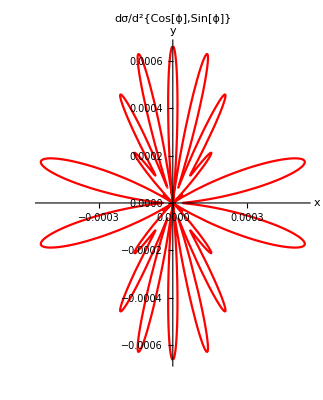

v_2=-0.0402007+0. ⅈ

```mathematica
x1u={0,1/2};
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=10.0;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

Conclusion : for large k_T, the two partons can be treated as independent and the soft gluon can be taken as radiated uncoherently from the two individual partons.

### kT<<1/r

-Graphics-

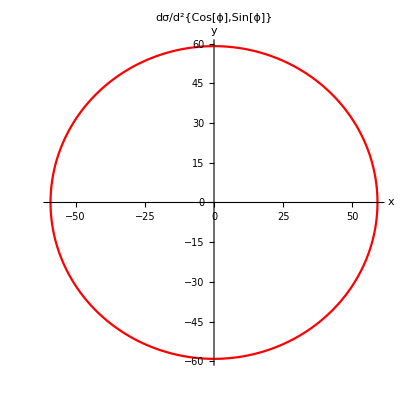

v_2=0.000347844+9.38067×10^-19 ⅈ

```mathematica
x1u={1/2,0};
x2u={-1/2,0};
x3u={1/2,0};
x4u={-1/2,0};
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

-Graphics-

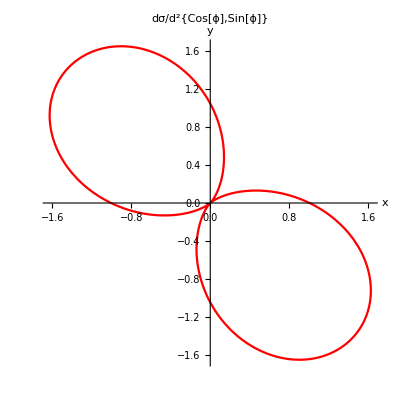

v_2=-0.0103349+8.84144×10^-19 ⅈ

-Graphics-

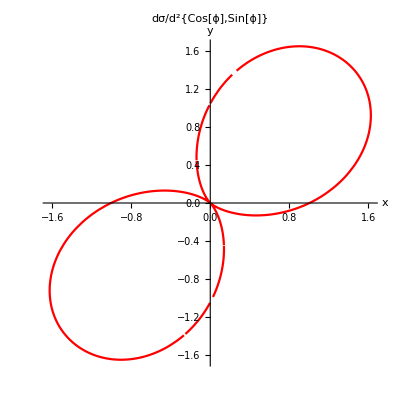

v_2=-0.0103349-2.30944×10^-19 ⅈ

```mathematica
x1u={1,1}/Sqrt[8];
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
x1u={-1,1}/Sqrt[8];
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

-Graphics-

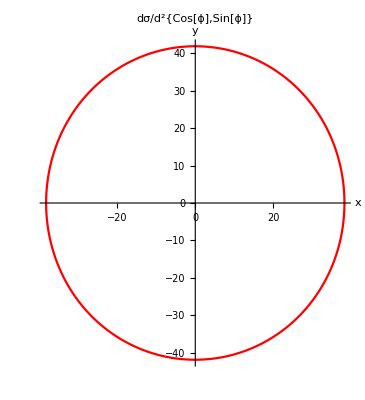

v_2=-0.0226608-1.3638×10^-18 ⅈ

```mathematica
x1u={0,1/2};
x2u=-x1u;
x3u=x1u;
x4u=-x1u;
bu={3,0};
kT=0.1;
showdσ[bu,x1u,x2u,x3u,x4u,kT]
```

Conclusion : for small k_T, radiation from the two partons can not distinguish the seperation of the dipole, hence v_2 is also negligible.